ACM40730 - Mathematica for Research

# Course Project

## Modelling the Trajectory of a Football from a Video using Object Recognition and Image Processing Techniques

Module Code:			ACM40730
Student Name :		Fanahan McSweeney
Student Number:		20203868
Submission Deadline:	18-Dec-20
Date of Submission :	14-Dec-20

## 1 Introduction

The aim of this project is to model and visualize the trajectory of a football by analysing a video of the ball being kicked. I would also like to compare two separate techniques that can be used when analysing a video, namely object recognition and image processing, and determine which is more suitable for this project.

Numerous examples of more advanced technology similar to what I am trying to achieve already exist and are widely used, such as Hawk-Eye and Toptracer. However, these systems are typically very expensive and require multiple high-speed cameras to implement, and as a result are not accessible to most people. For this project I will be using my current phone to record videos of a ball being kicked, using its 240fps slow motion capability. As most top end smart phones will have this capability, it is unlikely that an individual would require any additional hardware to implement this solution.

Due to the accessibility of this solution, it could potentially be used by anyone aiming to practice free kicks and goal kicks in sports such as soccer, Gaelic football and even rugby, even when limited to a small space for practice. It could also provide further insights into a person’s kicking technique by returning key metrics for each kick, such as speed, projected distance and projected flight time, and allow them to quantify their improvement.

There are a number of different methods that can be used to analyse images and video in Mathematica. This project will look at several image processing techniques that can be used to detect a circular object in an image. It will also look at some inbuilt object recognition functions in Mathematica, which will in this case allow us to identify a round ball in an image, but could potentially be used to track another object type such as a rugby ball.

## 2 Background

### 2.1 Calculating distance between the object and the camera

When analysing a single video of a football, it is relatively easy to estimate it’s trajectory in two dimensions. The horizontal and vertical movement of the ball between each frame can be calculated in pixels, and this can be converted to distances in metres if the size of the object and it’s distance from the camera is known. In this project, we will be analysing the trajectory of a ball in three dimensions, and we will consider the axes to be set up as in the image below. In a two dimensional case, we would only consider movement perpendicular to the camera in the horizontal direction and the vertical direction (i.e.in the x and y planes).

-Graphics3D-

When considering the three dimensional case, where a camera is set up facing towards the primary direction where the ball is travelling (i.e. in the z plane), the movement of the ball in the x and y planes can be tracked by looking at the x and y coordinates of the center of the ball in each frame. However, it isn’t possible to estimate the distance that the ball has travelled forwards, away from the camera (i.e. in the z plane), by looking at the x and y coordinates of the center of the ball.

To estimate the path of the ball in three dimensions, some additional steps need to be taken. To estimate movement in the z plane, we can look at the size of the object in each frame, and estimate the distance the object as travelled away from the camera.

In theory, the distance of the object from the camera could be calculated using the following equation:

distance to object (mm)_ = (f (mm) × real height (mm) × image height (pixels))/(object height (pixels) × sensor height (mm))

where 
	f is the focal length of the camera (in mm),
	real height is the real height of the object (in mm),
	image height is the height of the image (in pixels),
	object height is the height of the object within the image (in pixels),
	and sensor height is the sensor height of the camera (in mm).

While the real height, object height and image height are easy to obtain, obtaining the correct focal length and sensor height specifications for a camera can be difficult, in particular for a phone camera.

To overcome this issue, we can take another approach where we first calculate a perceived focal length for the camera, which we can then use to estimate the distance of an object from the camera. We can calculate the perceived focal length of a camera using the following equation:

f_perceived = (object height (pixels) × distance to object (m))/(real height (m))

where 
	f_perceived is the perceived focal length of the camera,
	real height is the real height of the object (in m),
	object height is the height of the object within the image (in pixels),
	and distance to object is the distance between the object and the camera (in m).

We can estimate the perceived focal length by taking a sample photo with the football, of known size, placed a known distance away from the camera, and using the equation above. To account for possible errors in the exact distance between the camera and the ball and also in the object height in the image measured by the software, we can take a number of sample photos with the football placed at varying distances from the camera, and then calculate the mean of all the perceived focal length calculated for each sample.

Once we have obtained a value for the perceived focal length, we can rearrange the formula above to calculate the distance between the ball and the camera from an image where the distance in not known:

distance to object (m) = (real height (m) × f_perceived)/(object height (pixels))

### 2.2 Converting vertical and horizontal movement from pixels to metres

Quantitatively measuring the vertical and horizontal movement of a football in a video is simply achieved by looking at the change in the the x and y position of the center of the ball in pixels between consecutive frames. However, to convert these changes in pixels to actual distances in metres, we need to take a number of factors into account.

#### 2.2.1 Centering the x-axis

By default, all pixel x and y coordinates in an image will have a positive value. For example, a pixel in the very first column of an image will have an x value of 1, and a pixel in the final column will have an x value equal to the image width in pixels.

For this project, it will be convenient to consider the centre of the camera’s field of view as the centre of the x-plane. This would require that all pixels left of the center of the image would be considered to have negative x values, and all pixels right of the center of the image would be considered to have positive x values. To achieve this, pixel x values can be modified using the following equation before any further calculations are performed:

new x (pixels) = original x (pixels) -(image width (pixels))/2

where 
	new x is the new value for x (pixels),
	original x is the original x coordinate value (pixels),
	and image width is the width of the image (pixels).

#### 2.2.2 Centering the y-axis

When considering the y axis, we will need to consider ground level as our zero reference level. However, it isn’t convenient to place the camera at ground level as it severely restricts the field of view of the camera. Instead, the camera can be set up at a known height above the ground, and we can factor this height into our calculations when determining the actual height of the ball above the ground in each frame.

if a camera is set up perpendicular to a perfectly level ground, then the centre of the camera’s field of view will be level with the height of the camera. Therefore if we look at any image captured on this camera, we can consider an object which is above the middle of the image as being above the height of the camera, and an object which is below the middle of the image as being below the height of the camera.

For this reason, and similar to the step taken for the x pixel values, we can also centre the y pixel values around the middle of the camera’s field of view using the following equation.

new y (pixels) = original y (pixels) -(image height (pixels))/2

where 
	new y is the new value for y (pixels),
	original y is the original y coordinate value (pixels),
	and image height is the height of the image (pixels).

As mentioned above, centering the y pixel values around the middle of the camera’s field of view will effectively be centering their values around the camera’s height above the ground. When calculating the actual height of the ball above ground level in a particular video frame, we will also need to take this camera height value into account, which will be done in section 2.2.3.

#### 2.2.3 Converting pixel values to real distances

For an object at a fixed distance away from the camera, we can calculate the distance that it travels between two consecutive video frames in both the x and y directions using variations of equations (2) and (3) above:

Δx real (m) = (distance to object (m) × Δx image (pixels))/f_perceived

Δy real (m) = (distance to object (m) × Δy image (pixels))/f_perceived

where 
	Δx real is the real distance travelled by the object in the x-axis between 2 video frames (m),
	Δx image is the change in the objects position in the image in the x-axis between 2 video frames (pixels),
	Δy real is the real distance travelled by the object in the y-axis between 2 video frames (m),
	Δy image is the change in the objects position in the image in the y-axis between 2 video frames (pixels),
	f_perceived is the perceived focal length of the camera,
	and distance to object is the distance between the object and the camera in both video frames (in m).

While the equations above hold for the case when there is no movement in the z-direction (i.e. the distance between the object and the camera is constant between both frames), in reality there will likely be some movement in the z-direction which we will need to account for. We can estimate the distances travelled in the case where there is movement in the z-direction by using the average value of the distance between the camera and the object in both frames, which gives us the following updated equations:

Δx real (m) = (((distance to object[1] (m) + distance to object[2] (m))/2) × Δx image (pixels))/f_perceived

Δy real (m) = (((distance to object[1] (m) + distance to object[2] (m))/2) × Δy image (pixels))/f_perceived

where 
	Δx real is the real distance travelled by the object in the x-axis between 2 video frames (m),
	Δx image is the change in the objects position in the image in the x-axis between 2 video frames (pixels),
	Δy real is the real distance travelled by the object in the y-axis between 2 video frames (m),
	Δy image is the change in the objects position in the image in the y-axis between 2 video frames (pixels),
	f_perceived is the perceived focal length of the camera,
	distance to object[1] is the distance between the object and the camera in the first video frames (in m),
	and distance to object[2] is the distance between the object and the camera in the second video frames (in m).

Finally, to calculate the actual distance travelled by the ball from the first frame of the video to the n^th frame, we need to sum all of the Δx real and Δy real from each consecutive video frame between frame 1 and frame n, which gives us the following equations:

distance travelled in x-direction (m) = ((distance to object[1] (m) × image x[1] (pixels))/f_perceived) +  ∑_(i=2)^n ((((distance to object[i-1]  (m) + distance 1 to object[i] (m))/2) × Δx image [i](pixels))/f_perceived)

distance travelled in y-direction (m)  = camera height (m) + ((distance to object[1] (m) × image y[1] (pixels))/f_perceived) +  ∑_(i=2)^n ((((distance to object[i-1]  (m) + distance 1 to object[i] (m))/2) ×  Δy image [i](pixels))/f_perceived)

where 
	image x[1] is the x-value of the object’s position in the first video frame (pixels),
	Δx image[i] is the change in the objects position in the image in the x-axis between the {i-1}^th and the i^th video frames (pixels),
	image y[1] is the y-value of the object’s position in the first video frame (pixels),
	Δy image[i] is the change in the objects position in the image in the y-axis between the {i-1}^th and the i^th video frames (pixels),
	camera height is the height of the camera above the ground,
	f_perceived is the perceived focal length of the camera,
	and distance to object[i] is the distance between the object and the camera in the i^th video frames (in m).

### 2.3 Calculating kick metrics

The trajectory of the ball can be modelled as a pair of second order polynomial parametric curves f[z] and g[z], where f[z] models the change in x values with respect to z, and g[z] models the change in y values with respect to z.

Once these curves have been determined, we can use them to calculating some useful metrics relating to the kick.

#### 2.3.1 Range

To calculate the maximum range of the ball in the z direction, we can look at the function g[z] which models the vertical position of the ball (i.e. y value) with respect to z. This function will equal to zero when the ball is at ground level, so solving for the roots of g[z]=0 will give two values for z where the ball is at ground level, which we can call z_max and z_min.

In general, for a function g[z] = a z^2+b z +c, the roots of g[z] = 0 will be:

z_min (m) = (-b  - √(b^2 - 4ac))/(2a)

z_max (m) = (-b  + √(b^2 - 4ac))/(2a)

We can then calculate the range of the kick using the following equation:

range (m) = z_min - z_max

#### 2.3.2 Maximum Height

The maximum height reached by the ball can again be determined using g[z], which models the change in vertical position of the ball with respect to z. The maximum height reached by the ball equates to the maximum value reached by g[z]. To determine this, we can take the derivative of g[z]. The maximum height will be the value of z which satisfies the equation g’[z]=0.

For a function g[z] = a z^2+b z +c, the derivative of g[z] equals:

g'[z] = 2az  + b

We can then evaluate g’[z]=0 to determine the maximum height reached by the ball:

max. height (m) = -b/(2a)

#### 2.3.3 Speed

To estimate the speed that the ball is travelling, we will need to know the frame rate that the input video was filmed at. Knowing this, we can calculate the amount of time that elapsed between any two specified frames in our video.

To estimate the distance travelled by the ball between two frames, we can calculate the arc length of the curve defined by our parametric equations f[z], g[z] and h[z], using the following equation:

arc length (m) = ∫_z_1^z_2 √((f'[z])^2+(g'[z])^2+(h'[z])^2)ⅆz

where
	z_1 is the value of z for the ball in the first frame (in metres),
	and z_2 is the value of z for the ball in the second frame (in metres).

In our case, as h[z] simply equals to z then h’[z] will equal 1, which we can use to simplify the above equation further.

The speed of the ball can then be estimated using the following equation:

speed (m/s) = (∫_z_1^z_2 √((f'[z])^2+(g'[z])^2+1)ⅆz)/(1/fps × (frame_2 index - frame_1 index))

where
	fps is the video frame rate in frames per second,
	frame_1 index is the index of the first video frame used,
	frame_2 index is the index of the second video frame used,
	z_1 is the value of z for the ball in the first frame,
	and z_2 is the value of z for the ball in the second frame.

#### 2.3.4 Flight time

Once the speed of the shot has been determined, the total time the ball is in the air can also be estimated. To do this we will need to consider the time taken for the ball the travel the full arc length of the curve defined by our parametric curves:

full arc length (m) = ∫_z_min^z_max √((f'[z])^2+(g'[z])^2+1)ⅆz

where
	z_min is the minimum value of z where the ball is at ground level (in metres),
	and z_max is the maximum value of z where the ball in at ground level (in metres).

We can then calculate the total time as the full arc length (in metres) divided by the average speed (in metres/second). This combines equations (18) and (19) to give the following equation:

full arc length (m) = (∫_z_min^z_max √((f'[z])^2+(g'[z])^2+ 1)ⅆz)/((∫_z_1^z_2 √((f'[z])^2+(g'[z])^2+1)ⅆz)/(1/fps × (frame_2 index - frame_1 index)))

## 3 Functions Used

A variety of different inbuilt Mathematica functions will be used to complete this project. Below, I have given a short summary of some of the most important of these functions.

### 3.1 Object Recognition

ImageContainsQ - takes an image and a category as an input, and returns True if an instance of the category is found in the image. In our case, we will be defining our category as a ball object.

Entity - represents an entity of a specified type. In our case, we will use this to define our category that will equate to a ‘ball’ of type ‘concept’. Instances of the Entity function will be seen in the following form throughout the project: "ball". If we look at the full form of this expression it returns the full definition: Entity[“Concept”,”Ball::qs4s5”].

ImageBoundingBoxes - returns a list of bounding boxes for each instance of the specified category in the input image. These boxes are returned in the form of Rectangle objects. Again, the Entity function will be used in conjunction with this to return bounding boxes for any ball found in an image.

### 3.2 Image Processing

ImageDifference - takes two images as input arguments and returns an image where each pixel is the absolute difference of the corresponding pixels in each image.

ColorDetect - returns a mask image representing all regions in an the input image near a specified color.

Binarize - creates a binary representation of the input image.

CommonestFilter - takes an image and a range value as inputs, and filters the image by replacing every pixel by the mean value of the specified range of neighbouring pixels.

ColorNegate - inverts all colors in an image.

Dilation - performs morphological dilation on an image.

SelectComponents - identifies components in an image that meet a specified criteria. To detect a filled circle, as we will be doing for this project, we can look for objects that meet a certain Eccentricity, BoundingDiskRadius and FilledCircularity.

ComponentMeasurements - computes measurements of specified properties of components in an image. We can find the centre coordinates and radius of components in an image (in pixels) by including the properties BoundingDiskCenter and BoundingDiskRadius.

### 3.3 Line fitting and working with polynomials

Fit - finds the least squares fit for the specified input data. We can specify the required form of the best fit line to be a quadratic equation by including {1, x, x^2} as the format.

Solve - solves an equation and returns its roots in a list of replacement rules. This can used to calculate the range for the ball instead of implementing the root equations (12) and (13) from section 2.3.1.

MaxValue - returns the maximum value of a function. This function can be used to calculate the maximum height in the football’s trajectory instead of implementing equation (16) from section 2.3.2.

ArcLength - returns the arc length of a parameterized curve between specified limits. Again, we can use this function when calculating the speed and total flight time of the ball rather than having to calculate the arc length of the curve using derivatives and integrals as shown in equations (18) and (20).

### 3.4 Plotting

ListPlot - plots a list of points with specified x and y coordinates.

ListLinePlot - plots a line through a list of points with specified x and y coordinates.

HighlightImage - highlights a specified region on an image. This can be used in conjunction with ImageBoundingBoxes to overlay bounding boxes over a ball in an image, or it can also be used with the Circle or Disk functions to draw a circle or disk with specified centre coordinates and radius on an image.

Plot - plots one or several functions over specified limits.

ParametricPlot - generates a 2D parametric plot of a curve. This can be used to plot 2D curves of trajectory of the ball when visualising it from specific angles.

ParametricPlot3D - generates a 3D parametric plot of a curve, which can be used to draw the final model of the trajectory of the football in 3 dimensional space.

Manipulate - allows the user to control a value or multiple values dynamically via sliders. This can be used in conjunction with various types of plots to visualise the change in the position of the ball over time. It is also possible to automatically modify values at a specified rate using the Animator and AnimationRate properties. We will be able to use these to animate the final 3D model of the ball’s trajectory to match the same speed calculated as the actual speed the ball was travelling at.

## 4 Methods and Analysis

### 4.1 Setup and Calibration

#### 4.1.1 Directory

A number of images and videos will need to imported into the notebook as part of this project. To ensure that they can be imported, the kernel directory must be set to the file path where they are stored. The files are saved in a folder named Data which is located in the same directory where the project notebook file is saved. The NotebookDirectory command returns the current notebook directory, so a string join can be used to append the data folder name on to the notebook directory name, and the SetDirectory command can then be used to set the kernel directory to the new path.

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
```

#### 4.1.2 Importing images for calibration

In order to estimate the distance between the football and the camera in each frame of our video, we can load in a number of different photos with the football set at different known distances from the camera, and in each case look at the size of the ball detected in the image (in pixels).

```mathematica
(*Import images individually*)
imgNoBall = Import["img_0.jpg"]; 
img1m = Import["img_1m.jpg"]; 
img2m = Import["img_2m.jpg"];  
img3m = Import["img_3m.jpg"];   
img4m = Import["img_4m.jpg"]; 
img5m = Import["img_5m.jpg"]; 

(*Create array of all test images*)
iArray = {img1m, img2m, img3m, img4m, img5m};
```

#### 4.1.3 Finding size and location of ball in test images - Image Processing

While both image processing and object recognition techniques will be tested in this project, the calibration steps will only be performed once for convenience. Either method could be used for this, but I have chosen to use image processing for this section.

The first image processing function used is ImageDifference which identifies the differences between our sample image containing the football and a reference image taken from the same position but with no ball included. This will remove the majority of the background detail in the image, leaving only the ball visible against a mostly black background. A major advantage of using this technique is that it prevents other round or circular objects that may be visible in the image from being identified as a ball.

If we use the ColorDetect function to detect anything in the photo with a colour near black, it will return a mask image in black an white, with the ball highlighted in black and the majority of the background in white.

```mathematica
img = iArray[[2]];
i1 = ImageDifference[imgNoBall, img];
i2 = ColorDetect[i1, Black];
GraphicsRow[{img,i1,i2}, ImageSize->600]
```

-Graphics-

We can then apply the Binarize function to convert the image into a true binary representation.

Next, we can apply the CommonestFilter function to the image. This filters the image by replacing each pixel with the mean pixel value within a specified range of neighbouring pixels, which removes the majority of noise from the image.

```mathematica
i3 = Binarize[i2];
i4 = CommonestFilter[i3, 6];
GraphicsRow[{i2,i3,i4}, ImageSize->600]
```

-Graphics-

The ColorNegate function can then be used to invert the color of the photo.

To fill in gaps that may exist on the object, the Dilation function can then be used.

```mathematica
i5 = ColorNegate[i4];
i6 = Dilation[i5,3];
GraphicsRow[{i4,i5,i6}, ImageSize->600]
```

-Graphics-

Finally, the SelectComponents function is used to detect components in the image that meet specified criteria. Here, we can specifies values for Eccentricity, BoundingDiskRadius and FilledCircularity which would meet the criteria of a circular object.

```mathematica
i7 = SelectComponents[i6, #Eccentricity < 0.6 && #BoundingDiskRadius > 20 && #FilledCircularity > 0.7 &];
GraphicsRow[{i6,i7}, ImageSize->400]
```

-Graphics-

We can extract measurements for any components within the resulting image using the ComponentsMeasurement function. To get the centre coordinates and radius of each component in the image, which in this case will be the ball.

Using the HighlightImage function, we can plot a circle with the same center and radius as the detected component over the original image. As we can see below, the circle lines up with the image of the ball.

```mathematica
components = ComponentMeasurements[i7, {"BoundingDiskCenter", "BoundingDiskRadius"}, #BoundingDiskRadius > 10 &][[1,2]]
HighlightImage[img, Circle[components[[1]],components[[2]]], ImageSize->200]
```

{{545.,597.},78.1313}

-Graphics-

To perform all of the above image processing steps in a single block of code, we can create a function called ipGetXYRvalues that takes a list of images, a reference image where there is no ball in the image, and returns the x, y and r values for any ball detected in each image. We will also return the index of the image.

```mathematica
ipGetXYRvalues[imgList_,imgRef_, increment_]:= 
Module[{img, i1, i2, i3, i4, i5, i6, i7, imgWidth, imgHeight, components},
	Table[
	img = imgList[[i]];
	{imgWidth, imgHeight} = ImageDimensions[img];
	
	i1 = ImageDifference[imgRef, img];
	i2 = ColorDetect[i1, Black];
	i3 = Binarize[i2];
	i4 = CommonestFilter[i3, 6];
	i5 = ColorNegate[i4];
	i6 = Dilation[i5, 3];
	i7 = SelectComponents[i6, #Eccentricity < 0.6 && #BoundingDiskRadius > 20 && #FilledCircularity > 0.7 &];
	
	components = ComponentMeasurements[i7, {"BoundingDiskCenter", "BoundingDiskRadius"}, #BoundingDiskRadius > 10 &];
	
	If[components≠{},
	{i, {components[[1,2,1,1]] - imgWidth/2, components[[1,2,1,2]] - imgHeight/2}, components[[1,2,2]]},
	Unevaluated@Sequence[]]
	
	,
	{i,1,Length[imgList],increment}]
]
```

```mathematica
sampleImgsXYR = ipGetXYRvalues[iArray,imgNoBall,1]
```

{{1,{-242.,-709.},158.885},{2,{5.,-363.},78.1313},{3,{8.161,-239.127},53.3797},{4,{35.1995,-173.996},40.6802},{5,{38.3643,-140.028},33.2336}}

#### 4.1.4 Estimating perceived focal length

To estimate the perceived focal length for the camera, we can utilise equation (2) from section 2.1.

First, we will create a list of heights of the ball in pixels in each of our test images. We can achieve this by extracting the radius value calculated for each image and multiplying it by 2.
Then we will create another list of numbers corresponding to the known distances in metres between the camera and the ball in each image. We will also create a variable that stores the actual height of the football in metres.

```mathematica
sampleImgsSizePix = (Transpose@sampleImgsXYR)[[3]] * 2
sampleImgsDistFromBall = {1.0, 2.0, 3.0, 4.0, 5.0}
ballRealHeight = 0.2 (*football measured as 20cm*)
```

{317.77,156.263,106.759,81.3604,66.4673}

{1.,2.,3.,4.,5.}

0.2

We will create a function that takes a list of sizes in pixels, a list of distances in metres and a real height value in metres, and returns the perceived focal length for each sample using equation (2).

```mathematica
fPerc[listSize_,listDist_,realHeight_]:= 
Table[
(listSize[[i]]* listDist[[i]])/realHeight,
{i,1,Length[listSize]}]
```

We can then apply this function to our new lists to calculate the perceived focal length for each of our sample images, and taking the mean of these values will give us our final estimation of the perceived focal length.

To visualize this, we can plot the perceived focal length for each sample image versus the distance from the camera to the object in the image, as well as a plot of the calculated mean value.

{1588.85,1562.63,1601.39,1627.21,1661.68}

1608.35

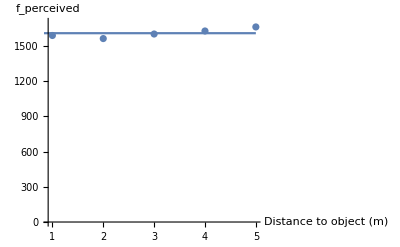

```mathematica
fPercList = fPerc[sampleImgsSizePix,sampleImgsDistFromBall,ballRealHeight]
Subscript[f, p] = Mean[fPercList]

Show[
ListPlot[Transpose@{sampleImgsDistFromBall, fPercList}, AxesLabel->{"Distance to object (m)","f_perceived"}, PlotRange->{0,Ceiling[Max[fPercList],100]}],
Plot[Subscript[f, p], {x,0,Max[sampleImgsDistFromBall]}]
]
```

### 4.2 Analysing video using Object Recognition techniques

#### 4.2.1 Importing video

Similar to importing images, we can also import videos into the notebook. You can click on the video below to view the football shot that we will attempt to model.

```mathematica
Import["vid_kick3.mp4"]
```

Video[/Users/fanahanmcsweeney/Projects/01-UCD-Autumn-Trimester/ACM40730-Mtica/FinalProject/Data/vid_kick3.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/fanahanmcsweeney/Projects/01-UCD-Autumn-Trimester/ACM40730-Mtica/FinalProject/Data/vid_kick3.mp4Thumbnail1StandardForm

We can import the video as a list of frames by including the ImageList argument in the Import function.

```mathematica
myVid = Import["vid_kick3.mp4", "ImageList"];
Length[myVid]
```

201

#### 4.2.2 Finding size and location of ball in video frames in pixels

Similar to when we looked at the sample images in section 4.1, we can use the ImageContainsQ function to determine which video frames a ball is detected in. As there are over 200 frames in the video being tested, it can be computationally expensive to look at every single frame. Instead, we can look at every 5th frame of the video to reduce computation time.

```mathematica
Total[Table[ ImageContainsQ[myVid[[i]],Entity["Concept","Ball::qs4s5"]], {i,1,Length[myVid],5}]]
```

7 False+34 True

Of the 41 video frames tested, a ball was detected in 34 of them. This should be more than sufficient for modeling the flight of the football in the video.

The ImageBoundingBoxes function will return coordinates of a bounding box containing the object specified in its arguments, in our case a ball. This is returned in the form of a Rectangle function. We can extract the rectangle coordinates returned by the ImageBoundingBoxes function and manipulate them to determine the equivalent x and y coordinates of the centre of the ball and the radius of the ball detected in an image.

First, to confirm that the function can correctly detect the ball in each frame, and that the rectangle coordinates returned correctly capture the ball, we can look at a few examples of frames from the video and apply the ImageBoundingBoxes function to them. We can then use the HighlightImage function to overlay the detected rectangle over the original image for each of the selected frames.

```mathematica
GraphicsRow[{
HighlightImage[myVid[[40]], ImageBoundingBoxes[myVid[[40]], Entity["Concept","Ball::qs4s5"]]],
HighlightImage[myVid[[90]], ImageBoundingBoxes[myVid[[90]], Entity["Concept","Ball::qs4s5"]]],
HighlightImage[myVid[[140]], ImageBoundingBoxes[myVid[[140]], Entity["Concept","Ball::qs4s5"]]]
}, ImageSize->750]
```

-Graphics-

The following function takes a list of images as an input argument, finds the rectangle coordinates for a ball in any images where a ball is detected, and calculates the equivalent x and y coordinates of the centre of the ball and the radius of the ball in each case. We will also adjust the x and y coordinates so the x and y plane are centered on the centre of each image, using equations (4) and (5) from section 2.2.

```mathematica
orGetXYRvalues[imgList_] := 
Module[{img,imgRect,x1,x2,y1,y2, xMid, yMid, r, imgWidth, imgHeight},
	{imgWidth, imgHeight} = ImageDimensions[imgList[[1]]];
	
	Table[
	img = imgList[[i]];
		If[
		ImageContainsQ[img,Entity["Concept","Ball::qs4s5"]],
		
		imgRect = ImageBoundingBoxes[img, Entity["Concept","Ball::qs4s5"]];
		x1 = imgRect[[1,1,1]]; x2 = imgRect[[1,2,1]];
		y1 = imgRect[[1,1,2]]; y2 = imgRect[[1,2,2]];
		xMid = (x1 + x2)/2 - imgWidth/2;
		yMid = (y1 + y2)/2 - imgHeight/2;
		r = ((x2 - x1)/2 + (y2 - y1)/2)/2;
		{i, {xMid, yMid}, r},
		 
		Unevaluated@Sequence[]
		],
	{i,1,Length[imgList],5}
	]
];
```

We can call this function with our imported video image list as the input argument to get the x, y and r values in pixels for the ball detected in each image.

```mathematica
orXYRpixels = orGetXYRvalues[myVid];
```

#### 4.2.3 Converting pixel values to real distances

In order to convert the x, y and radius values we have in pixels to meaningful distances in the x, y and z planes in metres, we can use equations from sections 2.1 and 2.2.3.

The function below takes three input arguments, a list of  x, y and radius coordinates, the real height of the object being observed, and the height of the camera above the floor. It then implements the equations (3), (10) and (11) to calculate the real movement of the object in the x, y and z directions between each video frame. This is done using a Table function for the z direction calculations, and using a combination of Table and Accumulation functions for the x and y direction calculations.

```mathematica
getXYZmetres[xyrList_, realObjectHeight_, cameraHeight_, fp_] := 
Module[{ind, xy, r, xM, yM, zM, x, y, z},
	
	{ind, xy, r} = Transpose[xyrList]; (* Extract inidices, x, y and radius values from input list *)
	
	(* Create list of all z values (i.e. distance between object and camera) in metres - equation (3) *)
	zM = Table[
		z = (realObjectHeight * fp)/(r[[i]] * 2),
		{i,1,Length[xyrList]}];
	
	(* Create list of all x values converted to metres - equation (10) *)
	xM = Accumulate[
			Table[
				If[i == 1,
				x = (zM[[1]] * xy[[1,1]])/fp,
				x = (((zM[[i-1]] + zM[[i]])/2) * (xy[[i,1]] - xy[[i-1,1]]))/fp]
			,	
			{i,1,Length[xyrList]}]];
			
	(* Create list of all y values converted to metres - equation (11) *)
	yM = Accumulate[
			Table[
				If[i == 1,
				y = cameraHeight + (zM[[1]] * xy[[1,2]])/fp,
				y = (((zM[[i-1]] + zM[[i]])/2) * (xy[[i,2]] - xy[[i-1,2]]))/fp]
			,	
			{i,1,Length[xyrList]}]];	
	
	Transpose@{ind, xM, yM, zM}
]
```

When this function is called with the list of x, y and r values in pixels calculated in section 4.2.2 as an input argument, it returns the real distances travelled by the ball between each video frame.

```mathematica
cameraHeight =  0.55; (* camera was set at 0.55m above ground *)
ballRealHeight = 0.22; (*football measured as 22cm*)

orXYZmetres = getXYZmetres[orXYRpixels, ballRealHeight, cameraHeight, Subscript[f, p]];
```

We can use list plots to visualise the distance travelled by the ball in the x and y directions relative to the distance the ball travelled in the z direction.

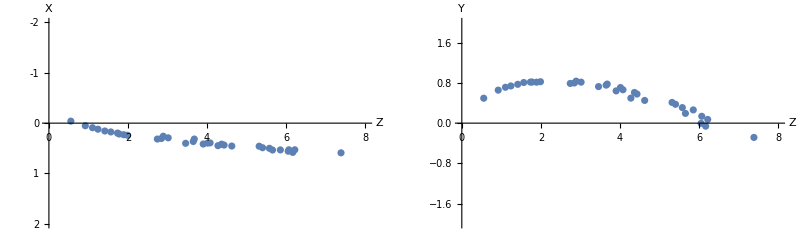

```mathematica
{orXYZmetresInd, orXYZmetresX, orXYZmetresY, orXYZmetresZ} = Transpose@orXYZmetres;
GraphicsRow[{
ListPlot[Transpose@{orXYZmetresZ,orXYZmetresX}, AxesLabel->{"Z","X"}, PlotRange->{{0,8},{-2,2}}, ScalingFunctions->"Reverse"],
ListPlot[Transpose@{orXYZmetresZ,orXYZmetresY}, AxesLabel->{"Z","Y"}, PlotRange->{{0,8},{-2,2}}]
}]
```

#### 4.2.4 Fitting our data to polynomials

To model the full flight path of the ball, we can fit our data to a pair of polynomial curves, the first to model the change in the x direction with respect to the z direction, and the second to model the change in the y direction with respect to the z direction. This will allow us to model the full flight of the ball with a video showing only a fraction of the ball’s full flight.

The Fit function can be used to fit a polynomial of a specified degree to a given set of data. For this project, I have chosen to fit both the x and y data to second order polynomials.

```mathematica
polyFit[xyzList_] := Module[{Ind, X, Y, Z, zMin, zMax, yData, yPoly, xData, xPoly},

{Ind, X, Y, Z} = Transpose@xyzList;

yData = Transpose@{Z, Y};
yPoly = Fit[yData, {1,z,z^2}, z];

{zMin,zMax} = z/.(Solve[yPoly==0, z]);

xData = Transpose@{Z, X};
xPoly = Fit[xData, {1,z,z^2}, z];

{xPoly, yPoly, xData, yData, zMin, zMax, Ind, X, Y, Z}
]
```

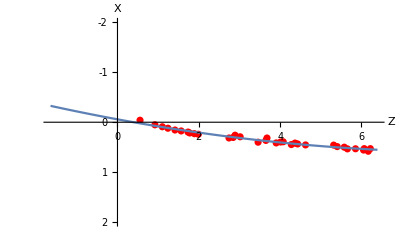

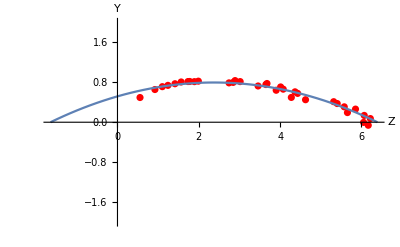

```mathematica
(*Extract the first 6 output parameters from the polyFit function*)
{orXYZmetresXpoly, orXYZmetresYpoly, orXYZmetresXdata, orXYZmetresYdata, orXYZmetresZmin, orXYZmetreszMax} = polyFit[orXYZmetres][[1;;6]];

(*Plot data and polynomial curve for x data versus z data*)
Show[
	ListPlot[orXYZmetresXdata, PlotStyle->Red, PlotRange->{{orXYZmetresZmin,orXYZmetreszMax},{-2,2}}, AxesLabel->{"Z", "X"}, ScalingFunctions->"Reverse"], 
	Plot[orXYZmetresXpoly, {z,orXYZmetresZmin,orXYZmetreszMax}, ScalingFunctions->"Reverse"]]

(*Plot data and polynomial curve for y data versus z data*)
Show[
	ListPlot[orXYZmetresYdata, PlotStyle->Red, PlotRange->{{orXYZmetresZmin,orXYZmetreszMax},{-2,2}}, AxesLabel->{"Z", "Y"}], 
	Plot[orXYZmetresYpoly, {z,orXYZmetresZmin,orXYZmetreszMax}]]
```

#### 4.2.5 Calculating kick metrics

Once we have modelled the flight of the ball, we can calculate some key metrics for the shot, such as speed, maximum height, range and total flight time. The equations used to calculate these metrics are defined in section 2.3.

To do this, we can create a function which takes a list containing the index, x, y and radius coordinates for each frame of a video (the format returned by the getXYZmetres function defined in section 4.2.3) and returns a number of metrics about the kick.

```mathematica
kickMetrics[xyzList_]:= 
Module[{xPoly, yPoly, xData, yData, zMin, zMax, Ind, X, Y, Z, shotRange, shotMaxHeight, shotSpeed, speedZ, shotFlightTime},

	{xPoly, yPoly, xData, yData, zMin, zMax, Ind, X, Y, Z} = polyFit[xyzList];	

	(* Shot range = difference between the 2 values where Z equals 0 *)
	shotRange = zMax - zMin;
	
	(* Shot max height = maximum value of our y polynomial *)
	shotMaxHeight = MaxValue[yPoly, z];
	
	(* Shot speed = average value of (arc length of parametric curves between z value at first frame and z value at last frame)/(1/fps × number of frames between first frame and last frame) *)
	shotSpeed = ArcLength[{xPoly, yPoly, z}, {z, First[Z], Last[Z]}]/(1/240 * (Last[Ind] - First[Ind]));
	
	(* We can now calculate the flight time of the shot as (arc length of parametric curves between z min and z max)/shotSpeed *)
	shotFlightTime = ArcLength[{xPoly, yPoly, z}, {z, zMin, zMax}]/shotSpeed;
	
	{shotRange, shotMaxHeight, shotSpeed, shotFlightTime}
]
```

We can call the kickMetrics function with our x, y and z values obtained in section 4.2.3.

```mathematica
{shotRange, shotMaxH, shotSpeed, shotTime} = kickMetrics[orXYZmetres];
```

```mathematica
Print["The range of the shot was ", Round[shotRange, 0.001], " m"]
Print["The maximum height reached by the shot was ", Round[shotMaxH, 0.001], " m"]
Print["The speed of the shot was ", Round[shotSpeed, 0.001], " m/s"]
Print["The total flight time of the shot was ", Round[shotTime, 0.001], " s"]
```

The range of the shot was 8.039 m

The maximum height reached by the shot was 0.796 m

The speed of the shot was 9.421 m/s

The total flight time of the shot was 0.881 s

### 4.3 Analysing video using Image Processing techniques

#### 4.3.1 Finding size and location of ball in video frames in pixels

Earlier in section 4.1.3 we defined a function ipGetXYRvalues to take a list of images and extract the x, y and radius values for a ball detected in each image. We can reuse this function to calculate these values for our imported video.

There is no ball in the first frame of our video, so we can enter this as the reference image to be used, and we can also give the increment input argument a value of 5 so the function will only analyse every fifth frame of the video, as was done when analysing the video using object recognition techniques.

```mathematica
ipXYRpixels = ipGetXYRvalues[myVid, myVid[[1]], 5];
```

#### 4.3.2 Converting pixel values to real distances

Again, the function getXYXmetres was previously defined in section 4.2.3, so we can call it again with the data obtained in section 4.3.1 as an input argument.

```mathematica
ipXYZmetres = getXYZmetres[ipXYRpixels, ballRealHeight, cameraHeight, Subscript[f, p]];
```

Again we can visualize the distance travelled by the ball in the x and y directions relative to the distance the ball travelled in the z direction using list plots.

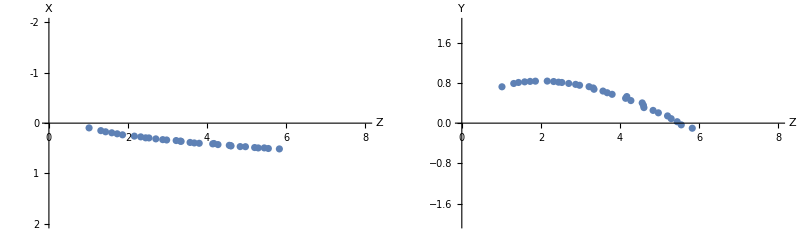

```mathematica
{ipXYZmetresInd, ipXYZmetresX, ipXYZmetresY, ipXYZmetresZ} = Transpose@ipXYZmetres;
GraphicsRow[{
ListPlot[Transpose@{ipXYZmetresZ,ipXYZmetresX}, AxesLabel->{"Z","X"}, PlotRange->{{0,8},{-2,2}}, ScalingFunctions->"Reverse"],
ListPlot[Transpose@{ipXYZmetresZ,ipXYZmetresY}, AxesLabel->{"Z","Y"}, PlotRange->{{0,8},{-2,2}}]
}]
```

#### 4.3.3 Fitting our data to polynomials

We can use the polyFit function defined earlier to fit our data to two second order polynomials. These can visualise how close these map to our data by plotting the curves and the data points on the same plot.

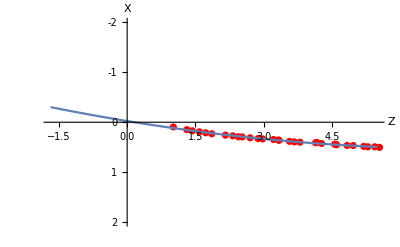

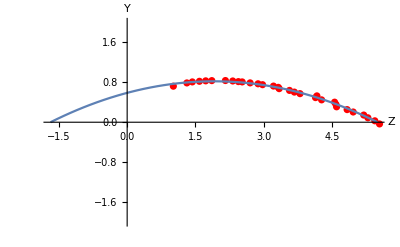

```mathematica
(*Extract the first 6 output parameters from the polyFit function*)
{ipXYZmetresXpoly, ipXYZmetresYpoly, ipXYZmetresXdata, ipXYZmetresYdata, ipXYZmetresZmin, ipXYZmetreszMax} = polyFit[ipXYZmetres][[1;;6]];

(*Plot data and polynomial curve for x data versus z data*)
Show[
	ListPlot[ipXYZmetresXdata, PlotStyle->Red, PlotRange->{{ipXYZmetresZmin,ipXYZmetreszMax},{-2,2}}, AxesLabel->{"Z", "X"}, ScalingFunctions->"Reverse"], 
	Plot[ipXYZmetresXpoly, {z,ipXYZmetresZmin,ipXYZmetreszMax}, ScalingFunctions->"Reverse"], ImageSize-> 400]

(*Plot data and polynomial curve for y data versus z data*)
Show[
	ListPlot[ipXYZmetresYdata, PlotStyle->Red, PlotRange->{{ipXYZmetresZmin,ipXYZmetreszMax},{-2,2}}, AxesLabel->{"Z", "Y"}], 
	Plot[ipXYZmetresYpoly, {z,ipXYZmetresZmin,ipXYZmetreszMax}], ImageSize-> 400]
```

#### 4.3.4 Calculating kick Metrics

Similarly, we can call the kickMetrics function defined in section 4.2.5 to calculate the metrics associated with the shot in our video.

```mathematica
{shotRange, shotMaxH, shotSpeed, shotTime} = kickMetrics[ipXYZmetres];
```

```mathematica
Print["The range of the shot was ", Round[shotRange, 0.001], " m"]
Print["The maximum height reached by the shot was ", Round[shotMaxH, 0.001], " m"]
Print["The speed of the shot was ", Round[shotSpeed, 0.001], " m/s"]
Print["The total flight time of the shot was ", Round[shotTime, 0.001], " s"]
```

The range of the shot was 7.188 m

The maximum height reached by the shot was 0.82 m

The speed of the shot was 7.254 m/s

The total flight time of the shot was 1.031 s

### 4.4 Comparing Object Recognition to Image Processing

There are various pros and cons associated with using both object recognition techniques and image processing techniques for identifying a football in an image.

#### 4.4.1 Precision

It is difficult to compare the performance of both techniques in terms of accuracy, particularly when there isn’t a significant difference in the results achieved by both. Even if we knew the the exact path that the ball actually travelled, without ensuring that our camera was set up exactly level and the and the distance between the ball and the camera in each of our calibration images was set up perfectly, there would inevitably be some error introduced into our model of the ball’s flight path.

We can however look at the precision of each technique, to determine if either of them give consistent results across the full range of the video.

Below, I have separated the index, x, y and z values obtained from both image processing and object recognition by transposing the relevant lists and extract each sublist as necessary.

```mathematica
{ipIndexVals, ipXVals, ipYVals, ipZVals} = Transpose@ipXYZmetres;
{orIndexVals, orXVals, orYVals, orZVals} = Transpose@orXYZmetres;
```

We can plot the x, y, and z values obtained for both techniques relative to the frame index value for both techniques using the ListLinePlot function. Below, the values obtained from image processing techniques are plotted in blue, while the values obtained using image recognition techniques are plotted in orange.

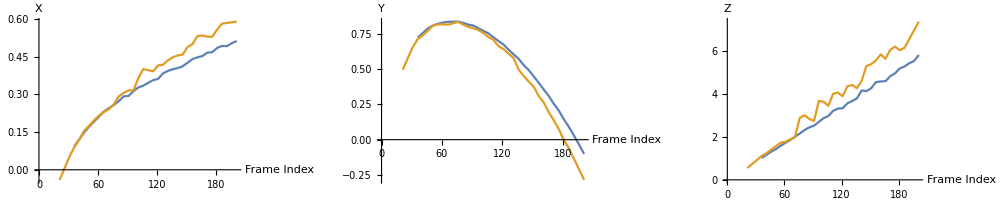

```mathematica
GraphicsRow[{
ListLinePlot[{Transpose@{ipIndexVals, ipXVals}, Transpose@{orIndexVals, orXVals}}, AxesLabel->{"Frame Index", "X"}],
ListLinePlot[{Transpose@{ipIndexVals, ipYVals}, Transpose@{orIndexVals, orYVals}}, AxesLabel->{"Frame Index", "Y"}],
ListLinePlot[{Transpose@{ipIndexVals, ipZVals}, Transpose@{orIndexVals, orZVals}}, AxesLabel->{"Frame Index", "Z"}]}, 
ImageSize->1000
]
```

We can see that the plots of the data obtained using image processing techniques (in blue) are smoother than those obtained using object recognition techniques (in orange). This is particularly evident in the third plot of the z values versus frame index, where the blue curve is a relatively smooth line in comparison to the orange curve where we can see large jumps in the data for z values greater than approximately 2.

We can also use the HighlightImage function to compare the circle coordinates calculated in each frame of the video using both techniques to the actual position of the ball in the frame. Below, I have set up two Manipulate functions, the first to look at the circle coordinates obtained using image processing and the second to look at the object recognition equivalent, so that we can view each frame of the video that was tested with the detected circle overlaid on the corresponding frame by dragging each slider. Similar to the plots above, we can see that the circles calculated using image processing appear to follow relatively closely to the actual size and position of the ball in each frame, whereas the circles obtained using object recognition don’t appear to match as closely, particularly the further away from the camera that the ball travels.

```mathematica
{imgWidthPixels, imgHeightPixels} = ImageDimensions[myVid[[1]]];
Row[{
	Manipulate[
		HighlightImage[myVid[[ ipXYRpixels[[ind,1]] ]], Circle[ {ipXYRpixels[[ind,2,1]]+imgWidthPixels/2, ipXYRpixels[[ind,2,2]]+imgHeightPixels/2}, ipXYRpixels[[ind,3]] ], ImageSize->500, PlotLabel->"Image Processing"]
	,{ind,1,Length[ipXYRpixels],1}],

	Manipulate[
		HighlightImage[myVid[[ orXYRpixels[[ind,1]] ]], Circle[ {orXYRpixels[[ind,2,1]]+imgWidthPixels/2, orXYRpixels[[ind,2,2]]+imgHeightPixels/2}, orXYRpixels[[ind,3]] ], ImageSize->500, PlotLabel->"Object Recognition"]
	,{ind,1,Length[orXYRpixels],1}]
}]
```

Therefore, it appears that using image processing techniques give more precise results than using object recognition, in particular for images where the ball is further than 2 metres away from the camera.

#### 4.4.2 Timing

Timing is also import when evaluating the performance of both techniques. We can use the Timing function to calculate the amount of time in seconds it takes to execute a specified line or block of code. Below we can test the length of time it takes to execute the orGetXYRvalues and ipGetXYRvalues functions on the imported video.

```mathematica
Timing[orGetXYRvalues[myVid];][[1]]
```

164.794

```mathematica
Timing[ipGetXYRvalues[myVid, myVid[[1]], 5];][[1]]
```

317.495

As we can see from the results, it takes under 3 minutes to execute the object recognition function on the video, while it takes over 5 minutes to execute equivalent function that uses image processing techniques. Clearly, using object recognition is far more efficient than using the image processing techniques used in this project, taking approximately half the time to execute the equivalent function.

### 4.5 Visualizing the data using plots

Based on the findings from section 4.4, I believe that, overall, the image processing method is preferable to the object recognition method for determining the position of the ball in each video frame. Therefore, I will use the values obtained from image processing techniques in section 4.3 when visualizing the data in plots in this section.

#### 4.5.1 Plotting circles obtained from image processing

Before looking at the projected flight of the ball in 3 dimensions, it may be useful to visualise the circle coordinates obtained from the image processing steps as described in section 4.1.3. Below, a Manipulate is used so we can vary the video frame we want to look at. The Graphics functions is used with Disk to plot a disk with centre and radius of the specified video frame, along with the Image function to plot the actual corresponding image. By adjusting the slider, we can see that the calculated circle coordinates do appear to match closely to the actual position of the ball.

```mathematica
{imgWidthPixels, imgHeightPixels} = ImageDimensions[myVid[[1]]];

Manipulate[
	Row[{
		Graphics[
			{EdgeForm[Blue], Yellow, Thick, 
			Disk[ ipXYRpixels[[ind,2]],ipXYRpixels[[ind,3]] ]},
			PlotRange->{{-imgWidthPixels/2,imgWidthPixels/2},{-imgHeightPixels/2,imgHeightPixels/2}},
			ImageSize->400],

		Image[myVid[[ ipXYRpixels[[ind,1]] ]], ImageSize->400]
	}]
	
,{ind,1,Length[ipXYRpixels],1}]
```

#### 4.5.2 3D model of the full flight path of the ball

To visualise the flight path of the ball in 3 dimensions, we will need to use the ParametricPlot3D function to plot our polynomial curves. Regardless of the input video used, it is unlikely that there will be more than ±2 metres of variation in the horizontal x plane, or that y values will exceed 3 metres. However there may be significantly more variance in the distance that the ball travels in the z plane. To account for this, we can automatically adjust the minimum and maximum z values based on the distance the projected range of the shot.

```mathematica
zMin = Floor[orXYZmetresZmin];
zMax = Ceiling[orXYZmetreszMax];

basic3Dplot[xPoly_, yPoly_, zMin_, zMax_]:=
	Show[
	ParametricPlot3D[
	{-xPoly, yPoly, z},{z,zMin,zMax},
	AxesOrigin->{0,0,0}, AxesLabel->{"X","Y","Z"}, 
	PlotRange->{{-2,2},{0,3},{zMin,zMax}}, BoxRatios->{1, 0.75, (zMax-zMin)/4},
	TicksStyle->8, Ticks->{Charting`ScaledTicks["Reverse"], Automatic, Automatic},
	ViewAngle->Automatic, ViewCenter->{0.5,0.5,0.5}, ViewMatrix->Automatic, ViewPoint->{-0.6,0.6,-2},
	ViewProjection->"Perspective", ViewRange->All, ViewVector->Automatic, ViewVertical->{-0.1,1,-0.11}],

	Graphics3D[{Green,Opacity[.2], InfinitePlane[{{0,0,1},{1,0,0},{1,0,1}}]}],
	ImageSize->400];
	
basic3Dplot[ipXYZmetresXpoly, ipXYZmetresYpoly, zMin, zMax]
```

-Graphics3D-

#### 4.5.3 Visualising the movement of the ball in 2D

To focus on certain elements of the flight of the ball, it can be useful to analyse it from different angle in 2 dimensional plots. For example, if we wanted to visualise how much the ball curled while in flight, we could isolate the flight of the ball to ignore the vertical y axis so that we could only see it’s movement in the x and z planes. This would  equate to a top down view of the flight of the ball.

We can create various different 2 dimensional plots visualising different viewpoints of the flight of the ball using Plot and ParametricPlot functions, as demonstrated below. I’ve also wrapped these plots in a Manipulate so that you can see the progression of the ball’s flight from each of the angle plotted by moving the slider.

```mathematica
multiView2Dplots[xPoly_,yPoly_, zMin_, zMax_]:= 
	Manipulate[
	Grid[{{
		ParametricPlot[{xPoly,z},{z,zMin,arc},
		PlotRange->{{-2,2},{Floor[zMin],Ceiling[zMax]}}, ImageSize->200, 
		AxesLabel->{"X","Z"}, PlotLabel->"Top down view of \nestimated path of football"],
		
		Plot[yPoly,{z,zMin,arc},
		PlotRange->{{Floor[zMin],Ceiling[zMax]},{0,2}}, ImageSize->350, AspectRatio->Automatic,
		AxesLabel->{"Z","Y"}, PlotLabel->"Side view of \nestimated path of football"],
		
		ParametricPlot[{xPoly,yPoly},{z,zMin,arc},
		PlotRange->{{-1,1},{0,2}}, ImageSize->300, 
		AxesLabel->{"X","Y"}, PlotLabel->"Front view of \nestimated path of football"]
	}}, Spacings->5]
	, {arc,zMin+0.001,zMax}, ContentSize->{1150, 500}];

multiView2Dplots[ipXYZmetresXpoly, ipXYZmetresYpoly, zMin, zMax]
```

#### 4.5.4 Animated 3D model of the flight of the ball

Finally, we can created a full animated 3D model of the kick using the Animator and AnimationRate properties of the Manipulate function. This will allow us to animate functions within a Manipulate automatically at a specified animation rate. As we have calculated the flight time and the distance travelled by the ball earlier, we can specify this rate so it actually animates at the predicted speed of the shot.

We can also add additional objects to our plot, such as a Sphere to represent the ball, which we can plot at the correct scale to the model, and also a Line which we can use to add a goalpost. We could potentially add any type of object that we wanted to the plot to assist with our shot analysis, such as additional targets to aim at, or a wall of players to be avoided for a free kick.

To make the model appear more realistic, I have also changed the plot background colour to a light blue similar to the sky, and I’ve also imported an image of a grass football pitch which I have applied to the plane defined at y=0 (i.e. the ground).

Similar to the 3D model created in section 4.5.2, we can change the viewing angle of the plot if we wish by pausing the animation and dragging it to the desired angle. This gives us the flexibility to visualise and analyse each modelled kick from any angle that we wish.

```mathematica
full3Dmodel[xPoly_, yPoly_, zMin_, zMax_, ballHeight_,shotTime_]:=

Manipulate[

Show[
ParametricPlot3D[
{-xPoly, yPoly, z},{z,zMin,arc},
AxesOrigin->{0,0,0}, PlotStyle->Green,
PlotRange->{{-2,2},{0,2},{Floor[zMin],Ceiling[zMax]}}, BoxRatios->{1, 0.5, (Ceiling[zMax]-Floor[zMin])/4},
TicksStyle->8, Ticks->{Charting`ScaledTicks["Reverse"], Automatic, Automatic}, Axes->False, Boxed->False,
ImageSize->550, ViewAngle->Automatic, ViewCenter->{0.5,0.5,0.5}, ViewMatrix->Automatic, ViewPoint->{5,5,-15},
ViewProjection->Automatic, ViewRange->All, ViewVector->Automatic, ViewVertical->{2,12,-2.5}, Background->LightBlue
],

(*Plot ball as a sphere*)
Graphics3D[{Yellow, Sphere[{-xPoly/.z->arc, yPoly/.z->arc, z/.z->arc}, (ballHeight/2)]}],
(*Plot goalpost as a line*)
Graphics3D[{White,Thickness[0.01], Line[{{-1,0,5},{-1,1,5},{1,1,5},{1,0,5}}]}],
(*Plot grass as a textured polygon*)
Graphics3D[ {Texture[Import["grass.jpg"]],Opacity[0.5], 
Polygon[{{-2,0,Floor[zMin]},{-2,0,Ceiling[zMax]},{2,0,Ceiling[zMax]},{2,0,Floor[zMin]}}, 
VertexTextureCoordinates->{{0,1,0},{1,1,0},{1,0,0},{0,0,0}}]}]
]

,{arc,zMin-5,zMax, Animator, AnimationRate->(zMax-zMin)/shotTime}, ContentSize->{570, 425}];

full3Dmodel[ipXYZmetresXpoly, ipXYZmetresYpoly, zMin, zMax, ballRealHeight, shotTime]
```

### 4.6 Combining techniques above to analyse another video

After the setup and calibration steps above are complete, ideally we would like to be able to analyse multiple videos of a football being kicked. If we want to process a different video using the techniques demonstrated above and analyse the flight of the football once again, it wouldn’t make sense to have to go back to the section where the first video was imported and execute all of the following steps once again.

Instead, we can define a function that takes a video name as an input argument, as well as a number of other calibration parameters such as the height of the ball and the height of the camera above the ground, and prints the metrics calculated for the kick as well as displaying some of the plots shown above to assist with analysing the kick.

```mathematica
modelFootballShot[videoString_, ballHeight_, cameraHeight_, fperc_]:=

Module[{vid, XYRpixels, XYZmetres, imgW, imgH, xPoly, yPoly, xData, yData, zMin, zMax, Ind, X, Y, Z, shotRange, shotMaxH,shotSpeed, shotTime, plotA1, plotB1, plotC1, plotD1},

	(*Import video as a list of images*)
	vid = Import[videoString, "ImageList"];
	
	(*Get x/y/r values in pixels for ball in each video frame*)
	XYRpixels = ipGetXYRvalues[vid, vid[[1]], 5];
	
	(*Convert x/y/r values in pixels to x/y/z values in metres*)
	XYZmetres = getXYZmetres[XYRpixels, ballHeight, cameraHeight, fperc];
	
	(*Fit x/y/z data to polynomials*)
	{xPoly, yPoly, xData, yData, zMin, zMax, Ind, X, Y, Z} = polyFit[XYZmetres];
	
	(*Calculate and print kick metrics*)
	{shotRange, shotMaxH, shotSpeed, shotTime} = kickMetrics[XYZmetres];
	Print["The range of the shot was ", Round[shotRange, 0.001], " m"];
	Print["The maximum height reached by the shot was ", Round[shotMaxH, 0.001], " m"];
	Print["The speed of the shot was ", Round[shotSpeed, 0.001], " m/s"];
	Print["The total flight time of the shot was ", Round[shotTime, 0.001], " s"];

	(*Calculate width/height of video frames in pixels*)
	{imgW,imgH} = ImageDimensions[vid[[1]]];
	
	(*Create function to plot circles detected in video frames using a manipualte*)
	diskPlot[XYR_, imgHeight_, imgWidth_, title_] := 
		Manipulate[
				Graphics[{EdgeForm[Blue], Yellow, Thick, Disk[ XYR[[ind,2]], XYR[[ind,3]] ]},
				PlotRange->{{-imgWidth/2,imgWidth/2},{-imgHeight/2,imgHeight/2}}, PlotLabel->title, ImageSize->400]
		,{ind,1,Length[XYR],1}];
			
	plotA1 = diskPlot[XYRpixels, imgH, imgW, "Circles detected in video frames"];
	
	(*Create basic 3D plot of the kick*)
	plotB1 = basic3Dplot[xPoly, yPoly, zMin, zMax];

	(*Create plots of 2D views of shot front different angles*)
	plotC1 = multiView2Dplots[xPoly, yPoly, zMin, zMax];

	plotD1 = full3Dmodel[xPoly, yPoly, zMin, zMax, ballHeight, shotTime];
	
		Column[{plotA1, plotB1, plotC1, plotD1}]
];
```

Before calling the function, we will import the video to be tested and take a quick look at it so that we can compare it to the plots that will be produced from the modelFootballShot function.

```mathematica
Import["vid_kick1.mp4"]
```

Video[/Users/fanahanmcsweeney/Projects/01-UCD-Autumn-Trimester/ACM40730-Mtica/FinalProject/Data/vid_kick1.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/fanahanmcsweeney/Projects/01-UCD-Autumn-Trimester/ACM40730-Mtica/FinalProject/Data/vid_kick1.mp4Thumbnail1StandardForm

If we now call this function with our new video included as an input, it will return the kick metrics and a number of different plots to help us visualize the trajectory of the ball.

```mathematica
modelFootballShot["vid_kick1.mp4", ballRealHeight, cameraHeight, Subscript[f, p]]
```

The range of the shot was 8.553 m

The maximum height reached by the shot was 0.951 m

The speed of the shot was 11.201 m/s

The total flight time of the shot was 0.793 s

-Graphics3D-

## 5 Conclusion

Based on the obtained results, I believe that it is possible to model the trajectory of a football from a video to a reasonable degree of accuracy using Mathematica. The proposed solution is relatively rudimentary and requires very precise set up and calibration to prevent significant errors from being introduced into the projected trajectory of the football, but considering the simplicity of the setup and the fact that it can be achieved using a standard smart phone, it appears to be possible to achieve satisfactory results using this method.

Mathematica has also been shown to be able to detect a ball in an image using different methods. The object recognition functionality available in Mathematica was very efficient in detecting a football in an image, although it was somewhat inconsistent when detecting the size of the ball in each image, particularly for images where the ball was relatively far away from the camera. One additional benefit of using object recognition is that it could potentially be used to detect objects other than a round ball.

The image processing techniques used were shown to produce relatively consistent results when identifying the position and size of a ball in an image, although it also took significantly longer to analyse an image using these techniques rather than using object recognition methods. However, only a limited amount of functions and combinations of functions were tested when using image processing to identify a ball in an image. Mathematica has a huge selection of functions that can be used for image processing, and it is likely that further development of this project would yield much more efficient results that what has currently been achieved.

Mathematica’s large selection of plotting functions also makes it an ideal tool for producing interesting and insightful plots to visually demonstrate the modelled trajectory of the ball.

## 6 References

[1] Rosebrock, Adrian. Find distance from camera to object/marker using Python and OpenCV. Retrived from https://www.pyimagesearch.com/2015/01/19/find-distance-camera-objectmarker-using-python-opencv/. Accessed 23^rd Nov. 2020.

[2] Dawkins, Paul. Arc Length With Vector Functions. Retrieved from https://tutorial.math.lamar.edu/classes/calciii/vectorarclength.aspx. Accessed on 23^rd Nov. 2020.

[3] Wolfram Mathematica. Built-in Object Detection & Recognition. Retrieved from https://www.wolfram.com/language/12/new-in-image-processing/built-in-object-detection-and-recognition.html?product=mathematica. Accessed on 25^th Nov. 2020.

[4] Mathematica Stack Exchange. How to find circular object in an image? Retrieved from https://mathematica.stackexchange.com/questions/11725/how-to-find-circular-objects-in-an-image. Accessed on 26^th Nov. 2020.

[5] Stack Overflow. Detect the circle and measure pixels. Retrieved from https://stackoverflow.com/questions/7831615/detect-the-circle-and-measure-pixels. Accessed 26^th Nov. 2020.

[6] Mathematica Stack Exchange. Flipping axes direction in Graphics3D. Retrieved from https://mathematica.stackexchange.com/questions/158480/flipping-axes-direction-in-graphics3d. Accessed on 29^th Nov. 2020.

[7] Narkive. How to find current ViewAngle, ViewPoint during Rotating graphics? Retrieved from https://comp.soft-sys.math.mathematica.narkive.com/fRqmXvtn/how-to-find-current-viewangle-viewpoint-during-rotating-graphics. Accessed on 29^th Nov. 2020.